# Modèle Murdoch LCT

## Generation of bifurcation diagram (script painful to use because the kernel frequently crashes when n is large)

Wearing 2004 parameters adapted for two host stages: 
	t_H1 = 37
	t_H2 = 5
	l = 21
	dH1 = 4.25e-3
	dH2 = 1/t_H2

	t_P1 = 20
	t_P2 = 2
	dP1 = .1
	dP2 = 1/t_P2
	a = .03
	
-> Rescaled by tH1 : 
	t_H1 = 1
	t_H2 = 5/37
	l = 21*37
	dH1 = 4.25e-3*37
	dH2 = 1/t_H2 *37

	t_P1 = 20/37
	t_P2 = 2/37
	dP1 = .1*37
	dP2 = 1/t_P2 *37
	a = .03*37

```mathematica
ClearAll;
SetDirectory[NotebookDirectory[]];
DATADIR = FileNameJoin[ParentDirectory[], "/data/raw"] ;

ODEkSystem[nn_, mm_]:=Module[{eqns,i},eqns={};
(*Équations pour H[i]*)Do[AppendTo[eqns,D[H[i][t],t]==(-θH-δH1-a P2[t]) H[i][t]+If[i>1,θH H[i-1][t],r H2[t]]],{i,1,nn}];
(*Équation pour H2*)AppendTo[eqns,D[H2[t],t]==θH H[nn][t]-δH2 H2[t]];
(*Équations pour P[i]*)Do[AppendTo[eqns,D[P[i][t],t]==(-θP-δP1) P[i][t]+If[i>1,θP P[i-1][t],a P2[t] H1[t]]],{i,1,mm}];
(*Équation pour P2*)AppendTo[eqns,D[P2[t],t]==θP P[nn][t]-δP2 P2[t]];
eqns];

(*Function to analyze a single solution*)
analyzeSolutionfreq[sol_,tMin_, tMax_, step_:.2]:=Module[{lastValues,lastts, mean,deviation,min,max, peaks, nbpeaks, Tpeak},
lastts= Table[t, {t, tMin, tMax, step}];
lastValues=Flatten[Table[H2[t]/.sol [[1]] // Evaluate,{t,tMin,tMax,step}],1];
(*If there's oscillation,return {min,max}*)
(*If stable equilibrium,return {equilibrium,equilibrium}*)
mean=Mean[lastValues];
deviation=StandardDeviation[lastValues];
min=Min[lastValues];
max=Max[lastValues];

(*Find peaks*)
peaks=FindPeaks[lastValues,Automatic, Automatic, (max-min)/4];(*peak higher than max-min/4 -> take only maxpeaks*)

(*just take the time between two arbitrary chosen peaks*)
Tpeak = lastts[[peaks[[4,1]]]]-lastts[[peaks[[3,1]]]];

(*If std dev is very small,it's likely a stable equilibrium*)If[min<0, {0,0,"error"},
If[deviation<0.01,{mean,mean,"equilibrium"},
{min,max,"limit_cycle", Tpeak}]]]

tH2par= 2;
tP1par = 1;
tP1parbis = 0.5;
θH = n*mH;
θP = m*mP;
r = ρ*δH2;

paramsplot = {mH->1,ρ -> 33,δH1->0,δH2->1/tH2par, mP->1/tP1parbis,δP2->8, δP1 -> 1, a-> 1};
paramsplotWearing = {mH->(1/37)//N,ρ -> 5*21//N,δH1->0.00425,δH2->1/5//N, mP->1/20//N,δP2->1/2//N, δP1 -> 0.1, a-> 0.03};
(*Define parameter range-using integers from 1 to 100 where n=m*)
nmValues=Join[Range[1,20], {30,40,50,100}]
```

{mH→1,ρ→33,δH1→0,δH2→1/2,mP→2.,δP2→8,δP1→1,a→1}

{mH→0.027027,ρ→105.,δH1→0.00425,δH2→0.2,mP→0.05,δP2→0.5,δP1→0.1,a→0.03}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,30,40,50,100}

## Tests de la fonction analyzeSolutionfreq

Point en haut à gauche

{mH→1,ρ→33,δH1→0,δH2→4.,mP→1/2,δP2→8,δP1→1,a→1}

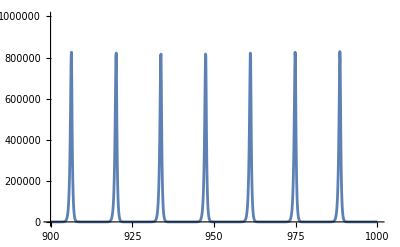

{0.0000395844,834915.,limit_cycle,13.8}

```mathematica
tMin = 800;
tMax = 1000;
tH2test = 0.25;
tP1test  = 2;
paramstest = {mH->1,ρ -> 33,δH1->0,δH2->1/tH2test, mP->1/tP1test,δP2->8, δP1 -> 1, a-> 1}
nn = 20;
mm = 20;
H1[t]= ∑_(i=1)^nn H[i][t];
P1[t]= ∑_(i=1)^mm P[i][t];
vars = Flatten[{Table[H[i][t],{i,1,nn}],H2[t],Table[P[i][t],{i,1,mm}], P2[t]}];
system = ODEkSystem[nn, mm];
θH = n*mH;
θP = m*mP;
r = ρ*δH2;

leqnIC = Flatten[{system, {H[1][0] == 10, Table[H[i][0] == 0,{i,2,nn}],H2[0] == 0,P[1][0] == 10, Table[P[i][0] == 0,{i,2,mm}], P2[0] == 0}}];
sol=NDSolve[leqnIC/.paramstest/.{n->nn,m->mm}/.{tH2->2, tP1->1},vars,{t, 0,tMax}];
ListLinePlot[Table[{t,H2[t]/. sol[[1]]}, {t, tMax-100, tMax,.1}],
PlotRange->{{tMax-100,tMax},{0,1000000}}
]
analyzeSolutionfreq[sol, tMin, tMax,.2]
```

Point en haut à droite

{mH→1,ρ→33,δH1→0,δH2→1/2,mP→1/2,δP2→8,δP1→1,a→1}

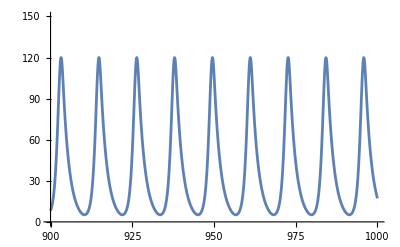

{5.1773,120.051,limit_cycle,11.6}

```mathematica
tMin = 800;
tMax = 1000;
tH2test = 2;
tP1test  = 2;
paramstest = {mH->1,ρ -> 33,δH1->0,δH2->1/tH2test, mP->1/tP1test,δP2->8, δP1 -> 1, a-> 1}
nn = 20;
mm = 20;
H1[t]= ∑_(i=1)^nn H[i][t];
P1[t]= ∑_(i=1)^mm P[i][t];
vars = Flatten[{Table[H[i][t],{i,1,nn}],H2[t],Table[P[i][t],{i,1,mm}], P2[t]}];
system = ODEkSystem[nn, mm];
θH = n*mH;
θP = m*mP;
r = ρ*δH2;

leqnIC = Flatten[{system, {H[1][0] == 10, Table[H[i][0] == 0,{i,2,nn}],H2[0] == 0,P[1][0] == 10, Table[P[i][0] == 0,{i,2,mm}], P2[0] == 0}}];
sol=NDSolve[leqnIC/.paramstest/.{n->nn,m->mm}/.{tH2->2, tP1->1},vars,{t, 0,tMax}];
ListLinePlot[Table[{t,H2[t]/. sol[[1]]}, {t, tMax-100, tMax,.1}],
PlotRange->{{tMax-100,tMax},{0,150}}
]
analyzeSolutionfreq[sol, tMin, tMax,.2]
```

Point en bas à droite

{mH→1,ρ→33,δH1→0,δH2→1/2,mP→2.,δP2→8,δP1→1,a→1}

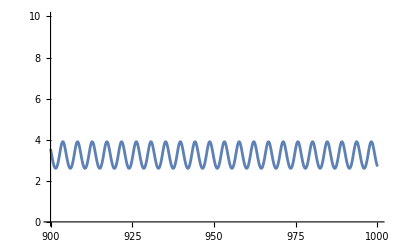

{2.60625,3.90369,limit_cycle,4.4}

```mathematica
tMin = 800;
tMax = 1000;
tH2test = 2;
tP1test  = 0.5;
paramstest = {mH->1,ρ -> 33,δH1->0,δH2->1/tH2test, mP->1/tP1test,δP2->8, δP1 -> 1, a-> 1}
nn = 20;
mm = 20;
H1[t]= ∑_(i=1)^nn H[i][t];
P1[t]= ∑_(i=1)^mm P[i][t];
vars = Flatten[{Table[H[i][t],{i,1,nn}],H2[t],Table[P[i][t],{i,1,mm}], P2[t]}];
system = ODEkSystem[nn, mm];
θH = n*mH;
θP = m*mP;
r = ρ*δH2;

leqnIC = Flatten[{system, {H[1][0] == 10, Table[H[i][0] == 0,{i,2,nn}],H2[0] == 0,P[1][0] == 10, Table[P[i][0] == 0,{i,2,mm}], P2[0] == 0}}];
sol=NDSolve[leqnIC/.paramstest/.{n->nn,m->mm}/.{tH2->2, tP1->1},vars,{t, 0,tMax}];
ListLinePlot[Table[{t,H2[t]/. sol[[1]]}, {t, tMax-100, tMax,.1}],
PlotRange->{{tMax-100,tMax},{0,10}}
]
analyzeSolutionfreq[sol, tMin, tMax,.2]
```

Point en bas à gauche

{mH→1,ρ→33,δH1→0,δH2→4.,mP→2.,δP2→8,δP1→1,a→1}

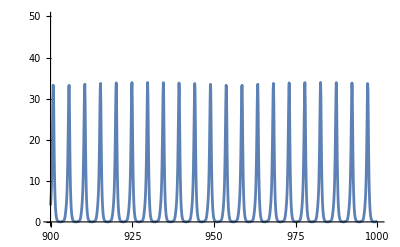

{0.0102984,33.9319,limit_cycle,4.8}

```mathematica
tMin = 800;
tMax = 1000;
tH2test = 0.25;
tP1test  = 0.5;
paramstest = {mH->1,ρ -> 33,δH1->0,δH2->1/tH2test, mP->1/tP1test,δP2->8, δP1 -> 1, a-> 1}
nn = 20;
mm = 20;
H1[t]= ∑_(i=1)^nn H[i][t];
P1[t]= ∑_(i=1)^mm P[i][t];
vars = Flatten[{Table[H[i][t],{i,1,nn}],H2[t],Table[P[i][t],{i,1,mm}], P2[t]}];
system = ODEkSystem[nn, mm];
θH = n*mH;
θP = m*mP;
r = ρ*δH2;

leqnIC = Flatten[{system, {H[1][0] == 10, Table[H[i][0] == 0,{i,2,nn}],H2[0] == 0,P[1][0] == 10, Table[P[i][0] == 0,{i,2,mm}], P2[0] == 0}}];
sol=NDSolve[leqnIC/.paramstest/.{n->nn,m->mm}/.{tH2->2, tP1->1},vars,{t, 0,tMax}];
ListLinePlot[Table[{t,H2[t]/. sol[[1]]}, {t, tMax-100, tMax,.1}],
PlotRange->{{tMax-100,tMax},{0,50}}
]
analyzeSolutionfreq[sol, tMin, tMax,.2]
```

Wearing mais avec les paramètres autres du Murdoch

```mathematica
tMin = 2500;
tMax = 3000;
tH2test = 0.135;
tP1test  = 0.540;
paramstest = {mH->1,ρ -> 33,δH1->0,δH2->1/tH2test, mP->1/tP1test,δP2->8, δP1 -> 1, a-> 1}
nn = 20;
mm = 20;
H1[t]= ∑_(i=1)^nn H[i][t];
P1[t]= ∑_(i=1)^mm P[i][t];
vars = Flatten[{Table[H[i][t],{i,1,nn}],H2[t],Table[P[i][t],{i,1,mm}], P2[t]}];
system = ODEkSystem[nn, mm];
θH = n*mH;
θP = m*mP;
r = ρ*δH2;

leqnIC = Flatten[{system, {H[1][0] == 10, Table[H[i][0] == 0,{i,2,nn}],H2[0] == 0,P[1][0] == 10, Table[P[i][0] == 0,{i,2,mm}], P2[0] == 0}}];
sol=NDSolve[leqnIC/.paramstest/.{n->nn,m->mm}/.{tH2->2, tP1->1},vars,{t, 0,tMax}];
ListLinePlot[Table[{t,H2[t]/. sol[[1]]}, {t, tMax-100, tMax,.1}],
PlotRange->{{tMax-100,tMax},{0,500}}
]
analyzeSolutionfreq[sol, tMin, tMax,.2]
```

{mH→1,ρ→33,δH1→0,δH2→7.40741,mP→1.85185,δP2→8,δP1→1,a→1}

Wearing avec tous les paramètres modifiés

{mH→1,ρ→105,δH1→0.15725,δH2→37/5,mP→37/20,δP2→37/2,δP1→3.7,a→1.11}

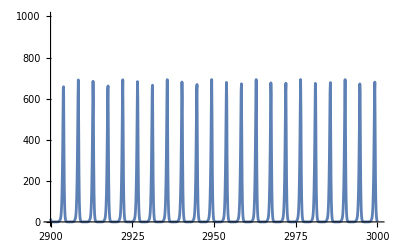

{0.00139015,692.948,limit_cycle,4.6}

```mathematica
tMin = 2500;
tMax = 3000;
paramstest = {mH->1,ρ -> (21*37)/(1/(5/37)),δH1->0.00425*37,δH2->1/(5/37), mP->1/(20/37),δP2->1/(2/37), δP1 -> .1*37, a-> .03*37}
nn = 20;
mm = 20;
H1[t]= ∑_(i=1)^nn H[i][t];
P1[t]= ∑_(i=1)^mm P[i][t];
vars = Flatten[{Table[H[i][t],{i,1,nn}],H2[t],Table[P[i][t],{i,1,mm}], P2[t]}];
system = ODEkSystem[nn, mm];
θH = n*mH;
θP = m*mP;
r = ρ*δH2;

leqnIC = Flatten[{system, {H[1][0] == 10, Table[H[i][0] == 0,{i,2,nn}],H2[0] == 0,P[1][0] == 10, Table[P[i][0] == 0,{i,2,mm}], P2[0] == 0}}];
sol=NDSolve[leqnIC/.paramstest/.{n->nn,m->mm},vars,{t, 0,tMax}];
ListLinePlot[Table[{t,H2[t]/. sol[[1]]}, {t, tMax-100, tMax,.1}],
PlotRange->{{tMax-100,tMax},{0,1000}}
]
analyzeSolutionfreq[sol, tMin, tMax,.2]
```

## Mesure des valeurs limites

```mathematica
Export[FileNameJoin[{Folder,"Murdoch_LCT_alternative_curves.csv"}],{}];
```

(équilibre stable ou min et max des cycles limites stables)

```mathematica
paramsplot = {mH->1,ρ -> 33,δH1->0,δH2->1/(0.25), mP->1/(2),δP2->8, δP1 -> 1, a-> 1}
(*nmValues={50};*)
tmax = 1000;
ComputingStatus = "Setup";
paramInfo=StringJoin[
"tH2_",ToString[1/(δH2/.paramsplot )//N],
"_tP1_",ToString[1/(mP/.paramsplot )//N],
"_rho_",ToString[ρ/.paramsplot ],
"_dP2_",ToString[δP2/.paramsplot ],
"_dH1_",ToString[δH1/.paramsplot ],
"_dP1_",ToString[δP1/.paramsplot ]
];
Folder="Murdoch_bifurcation_"<>paramInfo;
(*CreateDirectory[Folder];*)

(*Storage for results*)
bifurcationData={};
bifurcationDataDescriptor = {"n","m","eq or min or max", "stability type", "time between two peaks"};


(*Loop through parameter values*)
Monitor[
For[
i=1,i<=Length[nmValues],i++,Module[{currentN=nmValues[[i]],sol,analysis},(*Set up the system with current n=m value*)
ComputingStatus = "Setup";
nn=currentN;
mm=currentN;
H1[t]= ∑_(i=1)^nn H[i][t];
P1[t]= ∑_(i=1)^mm P[i][t];
vars = Flatten[{Table[H[i][t],{i,1,nn}],H2[t],Table[P[i][t],{i,1,mm}], P2[t]}];
system = ODEkSystem[nn, mm];
Clear[r, β];
θH = n*mH;
θP = m*mP;
r = ρ*δH2;

leqnIC = Flatten[{system, {H[1][0] == 10, Table[H[i][0] == 0,{i,2,nn}],H2[0] == 0,P[1][0] == 10, Table[P[i][0] == 0,{i,2,mm}], P2[0] == 0}}];
ComputingStatus = "Num resol";
sol=Check[
NDSolve[leqnIC/. paramsplot /.{n->nn,m->mm},vars,{t,0,tmax},
Method->{"StiffnessSwitching"},
StepMonitor:>(lastTime=t),
MaxSteps-> 100000],{"StiffnessError"}
];
ComputingStatus = "Sol analysis";
If[sol==={"StiffnessError"}||(ValueQ[lastTime]&&lastTime<tmax),Print["Failed"],
analysis=analyzeSolutionfreq[sol, tmax-200,tmax];
(*If[analysis[[3]]=="equilibrium",AppendTo[bifurcationData,{nn,mm,analysis[[1]],"equilibrium"}],
AppendTo[bifurcationData,{nn,mm,analysis[[1]], "min and time near min", analysis[[4]]}];
AppendTo[bifurcationData,{nn,mm,analysis[[2]],"max"}]];*)
;
filestr=OpenAppend[FileNameJoin[{Folder,"data.csv"}]];
If[analysis[[3]]=="equilibrium",
WriteString[filestr,ExportString[{{nn,mm, analysis[[1]], "equilibrium"}},"CSV"]],
WriteString[filestr,ExportString[{{nn,mm, analysis[[1]], "min and time near min", analysis[[4]]}},"CSV"]];
WriteString[filestr,ExportString[{{nn,mm,analysis[[2]],"max"}},"CSV"]]];
	Close[filestr];
];
]

],{i,Length[nmValues], ComputingStatus}
]
Export[FileNameJoin[{DATADIR, Folder,"nmRange.csv"}],nmValues];
Export[FileNameJoin[{DATADIR, Folder,"parameters.csv"}],paramsplot];
Export[FileNameJoin[{DATADIR,Folder,"description.csv"}],bifurcationDataDescriptor];
```

```mathematica
(*Create the bifurcation plot*)bifurcationPlot1=ListPlot[{(*Plot min values for limit cycles*)Select[bifurcationData,#[[4]]=="min and time near min"&][[All,{2,3}]],(*Plot max values for limit cycles*)Select[bifurcationData,#[[4]]=="max"&][[All,{2,3}]]},PlotStyle->{{PointSize[0.01],Blue},{PointSize[0.01],Red},{PointSize[0.01],Green}},
PlotLegends->{"Equilibrium","Cycle Min", "Cycle Max"},
PlotRange->All,
FrameLabel->{"CV of maturation time","min/max of H2 limit density"},PlotLabel->"Bifurcation Diagram for H2* ; tH2 = "<>ToString [tH2par]<>" ; tP1 = "<>ToString[tP1parbis],
ScalingFunctions->{"Log", "Log"},
Frame->True,GridLines->Automatic,ImageSize->Large] 

bifurcationPlot2=ListPlot[(*Plot equilibrium points*)
Select[bifurcationData,#[[4]]=="min and time near min"&][[All,{2,5}]],(*Plot max values for limit cycles*)
PlotStyle->{PointSize[0.01],Black},PlotLegends->{"T"},
FrameLabel->{"CV of maturation time","min/max of H2 limit density"},
ScalingFunctions->{"Log", None},
Frame->True,GridLines->Automatic,ImageSize->Large]
```

-Graphics-

-Graphics-

ListPlot::lpn: {{},{{0.693147180559945,-0.0925209},«4»,{«59»,-0.338952}},{{0.693147180559945,5.2552},{1.09861228866811,5.98311},{1.386294361119891,6.26449},{1.6094379124341,6.42036},{1.791759469228055,6.52188},{1.945910149055313,6.59552}}} is not a list of numbers or pairs of numbers.

ListPlot[{{},{{2,0.91163},{3,0.643137},{4,0.642666},{5,0.669387},{6,0.695091},{7,0.712517}},{{2,191.56},{3,396.672},{4,525.571},{5,614.225},{6,679.855},{7,731.812}}},PlotStyle→{{PointSize[0.01],RGBColor[0, 0, 1]},{PointSize[0.01],RGBColor[1, 0, 0]},{PointSize[0.01],RGBColor[0, 1, 0]}},PlotLegends→{Equilibrium,Cycle Min,Cycle Max},PlotRange→All,FrameLabel→{CV of maturation time,min/max of H2 limit density},PlotLabel→Bifurcation Diagram for H2* ; tH2 = 2 ; tP1 = 0.5,ScalingFunctions→{Log,Log},Frame→True,GridLines→Automatic,ImageSize→Large,PlotRange→{{0,100},{0,50}}]

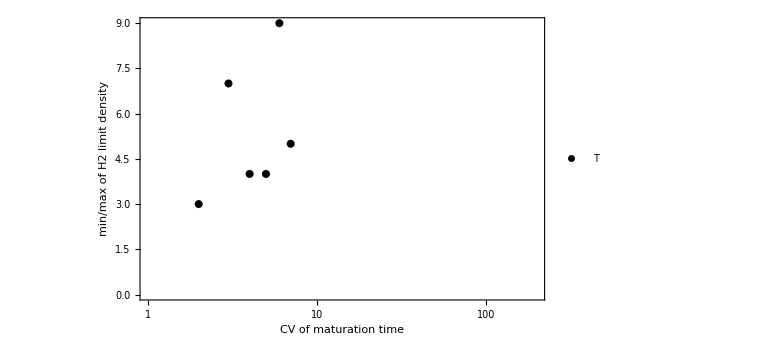

```mathematica
(*Create the bifurcation plot*)bifurcationPlot1=ListPlot[{(*Plot equilibrium points*)Select[bifurcationData,#[[4]]=="equilibrium"&][[All,{2,3}]],(*Plot min values for limit cycles*)Select[bifurcationData,#[[4]]=="min and time near min"&][[All,{2,3}]],(*Plot max values for limit cycles*)Select[bifurcationData,#[[4]]=="max"&][[All,{2,3}]]},PlotStyle->{{PointSize[0.01],Blue},{PointSize[0.01],Red},{PointSize[0.01],Green}},
PlotLegends->{"Equilibrium","Cycle Min", "Cycle Max"},
PlotRange->All,
FrameLabel->{"CV of maturation time","min/max of H2 limit density"},PlotLabel->"Bifurcation Diagram for H2* ; tH2 = "<>ToString [tH2par]<>" ; tP1 = "<>ToString[tP1parbis],
ScalingFunctions->{"Log", "Log"},
Frame->True,GridLines->Automatic,ImageSize->Large,
PlotRange->{{0,100},{0,50}}] 

bifurcationPlot2=ListPlot[(*Plot equilibrium points*)
Select[bifurcationData,#[[4]]=="min and time near min"&][[All,{2,5}]],(*Plot max values for limit cycles*)
PlotStyle->{PointSize[0.01],Black},PlotLegends->{"T"},
PlotRange->{{1,200},All},
FrameLabel->{"CV of maturation time","min/max of H2 limit density"},
ScalingFunctions->{"Log", None},
Frame->True,GridLines->Automatic,ImageSize->Large]
```

## Diagramme de caractérisation des oscillations (ne donne rien)

```mathematica
nn = 2;
mm = 2;
H1[t]= ∑_(i=1)^nn H[i][t];
P1[t]= ∑_(i=1)^mm P[i][t];
vars = Flatten[{Table[H[i][t],{i,1,nn}],H2[t],Table[P[i][t],{i,1,mm}], P2[t]}];
system = ODEkSystem[nn, mm];


tH2Min = .1;tH2Max = 3;tH2Pas = 0.2;
tP1Min = .1;tP1Max = 3;tP1Pas = 0.2;
tmax = 1500;
tlast = 1200;

Datasimu = {};

Monitor[
For[tH2val=tH2Min,tH2val<tH2Max,tH2val+=tH2Pas,
For[tP1val=tP1Min,tP1val<tP1Max,tP1val+=tP1Pas,

paramsplot = {mH->1,ρ -> 33,δH1->0,δH2->1/tH2val, mP->1/tP1val,δP2->8, δP1 -> 1, a-> 1};
leqnIC = Flatten[{system, {H[1][0] == 10, Table[H[i][0] == 0,{i,2,nn}],H2[0] == 0,P[1][0] == 10, Table[P[i][0] == 0,{i,2,mm}], P2[0] == 0}}];

sol=Check[
NDSolve[leqnIC/. paramsplot /.{n->nn,m->mm},vars,{t,0,tmax},
Method->{"StiffnessSwitching"},
StepMonitor:>(lastTime=t),
MaxSteps->50000],{"StiffnessError"}
];

If[sol==={"StiffnessError"}||(ValueQ[lastTime]&&lastTime<1000),Continue[],
lastAValues = Table[H2[t]/.sol[[1]], {t,tlast, tmax, 1}];
min = Min[lastAValues];
max = Max[lastAValues];
mean = Mean[lastAValues];
var = Variance[lastAValues];
peaks=FindPeaks[lastAValues,Automatic, Automatic, (max-min)/2];(*peak higher than max-min/2 -> take only maxpeaks*)
If[Dimensions[peaks][[1]] < 6, Tpeak1 = 0;Tpeak2=0;Tpeak3=0,
Tpeak1 = peaks[[4,1]]-peaks[[3,1]];
Tpeak2 = peaks[[5,1]]-peaks[[4,1]];
Tpeak3 = peaks[[6,1]]-peaks[[5,1]];
];
];

AppendTo[Datasimu,Flatten[{tH2val,tP1val,mean,var,min, max,Tpeak1,Tpeak2,Tpeak3}]];
Clear[lastTime];
]
],{tH2val, tP1val}
];
```

NDSolve::mxst: Maximum number of 50000 steps reached at the point t == 885.22.

NDSolve::mxst: Maximum number of 50000 steps reached at the point t == 1085.84.

NDSolve::mxst: Maximum number of 50000 steps reached at the point t == 1091.37.

General::stop: Further output of NDSolve::mxst will be suppressed during this calculation.

NDSolve::ndsz: At t == 433.591, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 297.948, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 43.1744, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

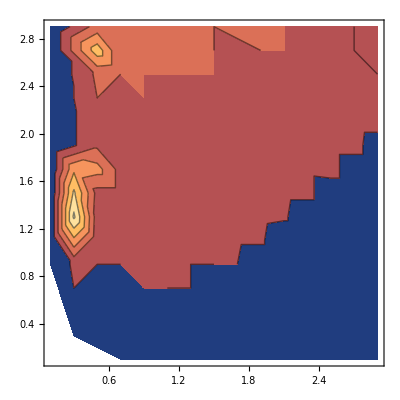

```mathematica
ListT = Datasimu[[All,{1,2,7}]];
ListContourPlot[ListT]
```

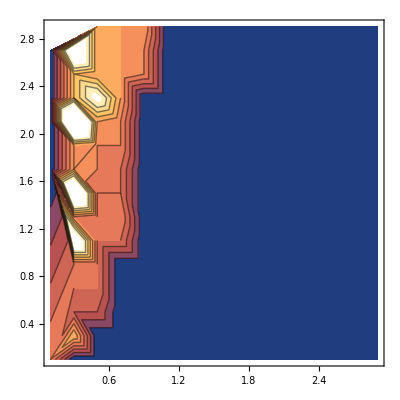

```mathematica
ListT = Datasimu[[All,{1,2,8}]];
ListContourPlot[ListT]
```

```mathematica
Datasimu
```

{{0.1,0.1,0.630839,0.790959,0.0143092,3.07735,7,5,7},{0.1,1.7,2.02469×10^-53,2.14621×10^-105,-5.15902×10^-66,1.8773×10^-52,0,0,0},{0.1,1.9,-2.41611×10^-52,1.47803×10^-103,-1.06169×10^-51,6.47587×10^-58,0,0,0},{0.1,2.1,2.54437×10^-50,2.63958×10^-99,-8.86006×10^-63,1.82389×10^-49,0,0,0},{0.1,2.3,2.338×10^-50,1.44159×10^-99,-1.14782×10^-62,1.06165×10^-49,0,0,0},{0.1,2.5,6.61062×10^-50,1.49846×10^-98,-3.69022×10^-62,3.89944×10^-49,0,0,0},{0.1,2.7,-4.7806×10^-54,1.0443×10^-106,-3.86239×10^-53,5.10208×10^-59,0,0,0},{0.3,0.1,0.784632,3.09918×10^-28,0.784632,0.784632,0,0,0},{0.3,0.3,1.3168,0.984396,0.328477,3.28074,2,7,2},{0.3,0.5,2.30609,6.76614,0.187229,8.56144,3,3,3},{0.3,0.7,3.73063,26.765,0.107217,18.0359,7,4,3},{0.3,0.9,5.58983,79.0018,0.0616078,32.4239,13,4,4},{0.3,1.1,7.72087,181.748,0.0361148,52.083,5,14,14},{0.3,1.3,10.24,370.995,0.0217561,76.7705,21,5,5},{0.3,1.5,12.9637,666.055,0.0135681,106.631,11,17,11},{0.3,1.7,15.4592,1077.95,0.00875968,141.108,6,6,6},{0.3,1.9,19.2446,1721.09,0.00584868,180.578,13,6,13},{0.3,2.1,22.3888,2515.83,0.0040254,225.888,7,20,7},{0.3,2.3,28.0305,4388.05,0.00285503,275.753,7,7,7},{0.3,2.5,30.0174,5124.32,0.00207884,329.535,15,7,22},{0.3,2.7,33.5792,6490.01,0.00155113,390.63,15,15,15},{0.5,0.1,1.30772,0.,1.30772,1.30772,0,0,0},{0.5,0.3,1.56867,8.38461×10^-28,1.56867,1.56867,0,0,0},{0.5,0.5,1.86926,0.0529883,1.56261,2.21389,2,3,3},{0.5,0.7,2.57382,2.05686,1.00791,5.20316,3,4,3},{0.5,0.9,3.48662,7.48595,0.819621,9.09276,4,4,3},{0.5,1.1,4.61677,19.5625,0.691794,14.4774,4,4,4},{0.5,1.3,5.99413,42.9337,0.594736,21.6017,5,4,4},{0.5,1.5,7.60392,84.4716,0.518227,30.5867,5,4,5},{0.5,1.7,9.50117,150.476,0.457651,41.3871,11,5,5},{0.5,1.9,11.3791,244.988,0.407236,54.6608,6,5,11},{0.5,2.1,13.7844,394.772,0.36686,69.012,5,6,6},{0.5,2.3,16.1686,578.885,0.332984,86.9482,6,11,6},{0.5,2.5,18.8339,851.481,0.305709,104.902,6,6,6},{0.5,2.7,21.6101,1182.86,0.281723,127.631,7,6,6},{0.5,2.9,24.7087,1634.77,0.261949,151.107,7,6,7},{0.7,0.1,1.83081,1.60471×10^-27,1.83081,1.83081,0,0,0},{0.7,0.3,2.19614,8.40798×10^-28,2.19614,2.19614,0,0,0},{0.7,0.5,2.59468,1.3231×10^-27,2.59468,2.59468,0,0,0},{0.7,0.7,3.02644,1.07591×10^-26,3.02644,3.02644,0,0,0},{0.7,0.9,3.49141,1.09398×10^-26,3.49141,3.49141,0,0,0},{0.7,1.1,3.98958,8.16848×10^-15,3.98958,3.98958,4,4,4},{0.7,1.3,4.69498,1.57565,3.12588,6.70277,4,5,4},{0.7,1.5,5.67706,7.10515,2.6627,10.3938,5,4,5},{0.7,1.7,6.84367,17.0654,2.44947,14.5798,5,4,5},{0.7,1.9,8.22582,37.4352,2.39867,19.4805,5,5,5},{0.7,2.1,9.56993,57.9665,2.22616,25.1798,6,5,5},{0.7,2.3,11.0652,92.9572,2.15977,31.7336,5,6,5},{0.7,2.5,12.7964,142.344,2.11092,39.1673,5,6,5},{0.7,2.7,14.6985,209.553,2.07401,47.5079,6,6,5},{0.7,2.9,16.6482,296.98,2.04681,56.7536,6,6,6},{0.9,0.1,2.3539,6.30622×10^-29,2.3539,2.3539,0,0,0},{0.9,0.3,2.82361,9.65392×10^-28,2.82361,2.82361,0,0,0},{0.9,0.5,3.33602,0.,3.33602,3.33602,0,0,0},{0.9,0.7,3.89113,3.909×10^-27,3.89113,3.89113,0,0,0},{0.9,0.9,4.48895,5.44991×10^-27,4.48895,4.48895,0,0,0},{0.9,1.1,5.12947,3.27158×10^-27,5.12947,5.12947,0,0,0},{0.9,1.3,5.81268,1.59636×10^-27,5.81268,5.81268,0,0,0},{0.9,1.5,6.5386,2.77792×10^-27,6.5386,6.5386,0,0,0},{0.9,1.7,7.30722,2.35123×10^-27,7.30722,7.30722,0,0,0},{0.9,1.9,8.11854,3.03764×10^-29,8.11854,8.11854,0,0,0},{0.9,2.1,8.97256,5.78164×10^-26,8.97256,8.97256,0,0,0},{0.9,2.3,9.86928,2.24073×10^-22,9.86928,9.86928,0,0,0},{0.9,2.5,10.8087,1.761×10^-7,10.8075,10.8098,6,5,6},{0.9,2.7,11.7971,0.149245,11.18,12.4194,6,5,6},{0.9,2.9,13.147,9.39073,9.26878,17.9749,5,6,6},{1.1,0.1,2.87698,2.1243×10^-28,2.87698,2.87698,0,0,0},{1.1,0.3,3.45108,1.88653×10^-27,3.45108,3.45108,0,0,0},{1.1,0.5,4.07736,0.,4.07736,4.07736,0,0,0},{1.1,0.7,4.75583,0.,4.75583,4.75583,0,0,0},{1.1,0.9,5.48649,1.66636×10^-28,5.48649,5.48649,0,0,0},{1.1,1.1,6.26935,1.27588×10^-26,6.26935,6.26935,0,0,0},{1.1,1.3,7.10439,7.13678×10^-27,7.10439,7.10439,0,0,0},{1.1,1.5,7.99162,5.61358×10^-27,7.99162,7.99162,0,0,0},{1.1,1.7,8.93105,6.36449×10^-27,8.93105,8.93105,0,0,0},{1.1,1.9,9.92266,0.,9.92266,9.92266,0,0,0},{1.1,2.1,10.9665,0.,10.9665,10.9665,0,0,0},{1.1,2.3,12.0625,1.26969×10^-26,12.0625,12.0625,0,0,0},{1.1,2.5,13.2106,6.41891×10^-28,13.2106,13.2106,0,0,0},{1.1,2.7,14.411,2.78626×10^-29,14.411,14.411,0,0,0},{1.1,2.9,15.6636,5.1132×10^-26,15.6636,15.6636,0,0,0},{1.3,0.1,3.40007,2.77785×10^-27,3.40007,3.40007,0,0,0},{1.3,0.3,4.07854,1.46824×10^-26,4.07854,4.07854,0,0,0},{1.3,0.5,4.8187,1.18953×10^-26,4.8187,4.8187,0,0,0},{1.3,0.7,5.62053,8.0578×10^-27,5.62053,5.62053,0,0,0},{1.3,0.9,6.48404,3.07284×10^-26,6.48404,6.48404,0,0,0},{1.3,1.1,7.40923,3.56944×10^-26,7.40923,7.40923,0,0,0},{1.3,1.3,8.3961,1.27896×10^-26,8.3961,8.3961,0,0,0},{1.3,1.5,9.44465,8.93453×10^-27,9.44465,9.44465,0,0,0},{1.3,1.7,10.5549,1.33512×10^-25,10.5549,10.5549,0,0,0},{1.3,1.9,11.7268,3.69671×10^-28,11.7268,11.7268,0,0,0},{1.3,2.1,12.9604,5.03836×10^-26,12.9604,12.9604,0,0,0},{1.3,2.3,14.2556,2.73139×10^-27,14.2556,14.2556,0,0,0},{1.3,2.5,15.6126,2.47032×10^-26,15.6126,15.6126,0,0,0},{1.3,2.7,17.0312,1.26437×10^-25,17.0312,17.0312,0,0,0},{1.3,2.9,18.5115,1.83335×10^-26,18.5115,18.5115,0,0,0},{1.5,0.1,3.92316,4.18582×10^-28,3.92316,3.92316,0,0,0},{1.5,0.3,4.70601,9.06364×10^-27,4.70601,4.70601,0,0,0},{1.5,0.5,5.56003,1.22986×10^-26,5.56003,5.56003,0,0,0},{1.5,0.7,6.48522,9.79957×10^-27,6.48522,6.48522,0,0,0},{1.5,0.9,7.48158,1.71538×10^-28,7.48158,7.48158,0,0,0},{1.5,1.1,8.54911,7.62576×10^-28,8.54911,8.54911,0,0,0},{1.5,1.3,9.6878,1.60988×10^-27,9.6878,9.6878,0,0,0},{1.5,1.5,10.8977,1.74321×10^-26,10.8977,10.8977,0,0,0},{1.5,1.7,12.1787,5.20964×10^-29,12.1787,12.1787,0,0,0},{1.5,1.9,13.5309,7.95269×10^-26,13.5309,13.5309,0,0,0},{1.5,2.1,14.9543,4.71269×10^-26,14.9543,14.9543,0,0,0},{1.5,2.3,16.4488,2.24847×10^-26,16.4488,16.4488,0,0,0},{1.5,2.5,18.0145,3.67117×10^-26,18.0145,18.0145,0,0,0},{1.5,2.7,19.6514,1.8679×10^-27,19.6514,19.6514,0,0,0},{1.5,2.9,21.3594,3.78666×10^-26,21.3594,21.3594,0,0,0},{1.7,0.1,4.44625,1.0863×10^-27,4.44625,4.44625,0,0,0},{1.7,0.3,5.33348,6.76671×10^-27,5.33348,5.33348,0,0,0},{1.7,0.5,6.30137,0.,6.30137,6.30137,0,0,0},{1.7,0.7,7.34992,4.28299×10^-27,7.34992,7.34992,0,0,0},{1.7,0.9,8.47913,4.76669×10^-26,8.47913,8.47913,0,0,0},{1.7,1.1,9.68899,1.85727×10^-27,9.68899,9.68899,0,0,0},{1.7,1.3,10.9795,2.06309×10^-27,10.9795,10.9795,0,0,0},{1.7,1.5,12.3507,1.23397×10^-26,12.3507,12.3507,0,0,0},{1.7,1.7,13.8025,0.,13.8025,13.8025,0,0,0},{1.7,1.9,15.335,0.,15.335,15.335,0,0,0},{1.7,2.1,16.9482,8.27194×10^-26,16.9482,16.9482,0,0,0},{1.7,2.3,18.642,6.28266×10^-27,18.642,18.642,0,0,0},{1.7,2.5,20.4164,1.3205×10^-26,20.4164,20.4164,0,0,0},{1.7,2.7,22.2716,7.68611×10^-27,22.2716,22.2716,0,0,0},{1.7,2.9,24.2074,1.50448×10^-25,24.2074,24.2074,0,0,0},{1.9,0.1,4.96934,0.,4.96934,4.96934,0,0,0},{1.9,0.3,5.96095,1.09092×10^-27,5.96095,5.96095,0,0,0},{1.9,0.5,7.04271,0.,7.04271,7.04271,0,0,0},{1.9,0.7,8.21462,5.62383×10^-27,8.21462,8.21462,0,0,0},{1.9,0.9,9.47667,2.34387×10^-26,9.47667,9.47667,0,0,0},{1.9,1.1,10.8289,1.425×10^-28,10.8289,10.8289,0,0,0},{1.9,1.3,12.2712,6.68113×10^-28,12.2712,12.2712,0,0,0},{1.9,1.5,13.8037,1.05768×10^-26,13.8037,13.8037,0,0,0},{1.9,1.7,15.4264,6.34234×10^-28,15.4264,15.4264,0,0,0},{1.9,1.9,17.1391,0.,17.1391,17.1391,0,0,0},{1.9,2.1,18.9421,1.96391×10^-27,18.9421,18.9421,0,0,0},{1.9,2.3,20.8352,4.76482×10^-26,20.8352,20.8352,0,0,0},{1.9,2.5,22.8184,3.10096×10^-27,22.8184,22.8184,0,0,0},{1.9,2.7,24.8918,0.,24.8918,24.8918,0,0,0},{1.9,2.9,27.0553,4.8612×10^-26,27.0553,27.0553,0,0,0},{2.1,0.1,5.49242,1.37314×10^-29,5.49242,5.49242,0,0,0},{2.1,0.3,6.58842,8.81578×10^-29,6.58842,6.58842,0,0,0},{2.1,0.5,7.78405,1.11755×10^-29,7.78405,7.78405,0,0,0},{2.1,0.7,9.07931,2.91742×10^-28,9.07931,9.07931,0,0,0},{2.1,0.9,10.4742,3.32195×10^-28,10.4742,10.4742,0,0,0},{2.1,1.1,11.9688,4.4707×10^-27,11.9688,11.9688,0,0,0},{2.1,1.3,13.5629,0.,13.5629,13.5629,0,0,0},{2.1,1.5,15.2567,1.27138×10^-27,15.2567,15.2567,0,0,0},{2.1,1.7,17.0502,1.58173×10^-26,17.0502,17.0502,0,0,0},{2.1,1.9,18.9433,1.20887×10^-27,18.9433,18.9433,0,0,0},{2.1,2.1,20.936,3.42387×10^-28,20.936,20.936,0,0,0},{2.1,2.3,23.0283,2.52322×10^-27,23.0283,23.0283,0,0,0},{2.1,2.5,25.2203,1.84783×10^-28,25.2203,25.2203,0,0,0},{2.1,2.7,27.5119,0.,27.5119,27.5119,0,0,0},{2.1,2.9,29.9032,7.73589×10^-27,29.9032,29.9032,0,0,0},{2.3,0.1,6.01551,3.04614×10^-27,6.01551,6.01551,0,0,0},{2.3,0.3,7.21589,1.52833×10^-27,7.21589,7.21589,0,0,0},{2.3,0.5,8.52539,2.1457×10^-30,8.52539,8.52539,0,0,0},{2.3,0.7,9.94401,1.49077×10^-27,9.94401,9.94401,0,0,0},{2.3,0.9,11.4718,6.62671×10^-27,11.4718,11.4718,0,0,0},{2.3,1.1,13.1086,1.09199×10^-28,13.1086,13.1086,0,0,0},{2.3,1.3,14.8546,1.23483×10^-29,14.8546,14.8546,0,0,0},{2.3,1.5,16.7098,2.45906×10^-27,16.7098,16.7098,0,0,0},{2.3,1.7,18.674,3.49202×10^-28,18.674,18.674,0,0,0},{2.3,1.9,20.7474,0.,20.7474,20.7474,0,0,0},{2.3,2.1,22.9299,3.70585×10^-26,22.9299,22.9299,0,0,0},{2.3,2.3,25.2215,6.87927×10^-26,25.2215,25.2215,0,0,0},{2.3,2.5,27.6223,4.97719×10^-29,27.6223,27.6223,0,0,0},{2.3,2.7,30.1321,0.,30.1321,30.1321,0,0,0},{2.3,2.9,32.7511,4.88417×10^-26,32.7511,32.7511,0,0,0},{2.5,0.1,6.5386,0.,6.5386,6.5386,0,0,0},{2.5,0.3,7.84336,1.62497×10^-28,7.84336,7.84336,0,0,0},{2.5,0.5,9.26672,0.,9.26672,9.26672,0,0,0},{2.5,0.7,10.8087,6.21587×10^-27,10.8087,10.8087,0,0,0},{2.5,0.9,12.4693,4.85508×10^-27,12.4693,12.4693,0,0,0},{2.5,1.1,14.2485,7.41008×10^-27,14.2485,14.2485,0,0,0},{2.5,1.3,16.1463,4.00231×10^-26,16.1463,16.1463,0,0,0},{2.5,1.5,18.1628,7.44313×10^-26,18.1628,18.1628,0,0,0},{2.5,1.7,20.2978,1.67966×10^-26,20.2978,20.2978,0,0,0},{2.5,1.9,22.5515,0.,22.5515,22.5515,0,0,0},{2.5,2.1,24.9238,3.05741×10^-28,24.9238,24.9238,0,0,0},{2.5,2.3,27.4147,5.93996×10^-26,27.4147,27.4147,0,0,0},{2.5,2.5,30.0242,1.49613×10^-26,30.0242,30.0242,0,0,0},{2.5,2.7,32.7523,5.45697×10^-26,32.7523,32.7523,0,0,0},{2.5,2.9,35.599,7.80909×10^-26,35.599,35.599,0,0,0},{2.7,0.1,7.06169,2.48816×10^-27,7.06169,7.06169,0,0,0},{2.7,0.3,8.47082,3.33593×10^-28,8.47082,8.47082,0,0,0},{2.7,0.5,10.0081,2.23903×10^-27,10.0081,10.0081,0,0,0},{2.7,0.7,11.6734,1.29659×10^-27,11.6734,11.6734,0,0,0},{2.7,0.9,13.4668,5.9174×10^-28,13.4668,13.4668,0,0,0},{2.7,1.1,15.3884,1.04972×10^-26,15.3884,15.3884,0,0,0},{2.7,1.3,17.438,2.76134×10^-26,17.438,17.438,0,0,0},{2.7,1.5,19.6158,1.32121×10^-26,19.6158,19.6158,0,0,0},{2.7,1.7,21.9217,1.03557×10^-27,21.9217,21.9217,0,0,0},{2.7,1.9,24.3556,2.34773×10^-26,24.3556,24.3556,0,0,0},{2.7,2.1,26.9177,1.99422×10^-26,26.9177,26.9177,0,0,0},{2.7,2.3,29.6079,2.40343×10^-26,29.6079,29.6079,0,0,0},{2.7,2.5,32.4261,2.07845×10^-26,32.4261,32.4261,0,0,0},{2.7,2.7,35.3725,9.41716×10^-26,35.3725,35.3725,0,0,0},{2.7,2.9,38.447,2.34881×10^-26,38.447,38.447,0,0,0},{2.9,0.1,7.58478,6.23067×10^-27,7.58478,7.58478,0,0,0},{2.9,0.3,9.09829,3.03596×10^-28,9.09829,9.09829,0,0,0},{2.9,0.5,10.7494,9.54622×10^-27,10.7494,10.7494,0,0,0},{2.9,0.7,12.5381,1.77958×10^-27,12.5381,12.5381,0,0,0},{2.9,0.9,14.4644,3.95917×10^-27,14.4644,14.4644,0,0,0},{2.9,1.1,16.5283,3.92251×10^-26,16.5283,16.5283,0,0,0},{2.9,1.3,18.7298,1.2451×10^-27,18.7298,18.7298,0,0,0},{2.9,1.5,21.0688,1.68658×10^-26,21.0688,21.0688,0,0,0},{2.9,1.7,23.5455,1.69698×10^-26,23.5455,23.5455,0,0,0},{2.9,1.9,26.1597,0.,26.1597,26.1597,0,0,0},{2.9,2.1,28.9116,1.41735×10^-26,28.9116,28.9116,0,0,0},{2.9,2.3,31.801,5.88187×10^-27,31.801,31.801,0,0,0},{2.9,2.5,34.8281,5.87702×10^-26,34.8281,34.8281,0,0,0},{2.9,2.7,37.9927,2.96317×10^-26,37.9927,37.9927,0,0,0},{2.9,2.9,41.2949,1.33151×10^-27,41.2949,41.2949,0,0,0}}